# Gif generator for SPH - 2D Stars

```mathematica
SetDirectory[NotebookDirectory[]];
output=Normal[RunProcess["make","StandardOutput"]];
start=Flatten@StringPosition[output,"start"];
end=Flatten@StringPosition[output,"end"];
a=ToExpression@StringTake[output,{start⟦2⟧+1,end⟦1⟧-1}]; (*output must be in form
								"start"{(time 0){(particle 1){x,y,ρ}, (particle 2){x,y,ρ},…},(time 1){…},…}"end"  *)
teste={};
```

$Aborted

StringPosition::strse: String or list of strings expected at position 1 in StringPosition[output,start].

StringPosition::strse: String or list of strings expected at position 1 in StringPosition[output,end].

StringTake::strse: String or list of strings expected at position 1 in StringTake[output,{1+start,-1+output}].

ToExpression::notstrbox: StringTake[output,{1+start,-1+output}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

```mathematica
Do[
b=a⟦i,All,{1,2}⟧;
c=Flatten@a⟦i,All,{3}⟧;

pos=a⟦i,All,{1,2}⟧;
density=Flatten@a⟦i,All,{3}⟧;
colorf=Blend[{Blue,Red},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{ Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,PlotLabel->"ρ/ρ_max",FrameTicks->None,PlotRangePadding->.5];

AppendTo[teste,Graphics[{Point[pos,VertexColors->colorf/@Rescale@density],Text["t = "<>ToString[i],Scaled[{1.1,1}]],Inset[plotLegend[{Min@#,Max@#}&@density,20,colorf],Scaled[{5/5,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]},Frame->True,Axes->True,AxesOrigin->{-1,-1},ImageSize->Large,PlotRange->{{-1,1},{-1,1}},ImagePadding->{{Automatic, 100}, {Automatic, 1}},PlotLabel->"Time evolution of a 2D Star"]];

,{i,1,(Dimensions@a)[[1]]}]
```

```mathematica
Animate[teste⟦i⟧,{i,1,400,1},AnimationRate->10]
```

```mathematica
Export["finalperhaps.gif",teste[[1;;400]],"GIF"(*,"DisplayDurations"-> ConstantArray[0.5,Length@teste]*)]
```

finalperhaps.gif

```mathematica
profile=Import["rho_profile.dat"];
m=Fit[profile,{1,x,x^2},x]
```

1.00752-0.454471 x-8.83799 x^2

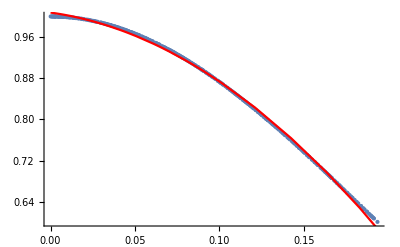

```mathematica
Show[ListPlot[profile],Plot[m,{x,0,1},PlotStyle->Red]]
```

```mathematica
(Dimensions@a)⟦1⟧-1
```

2000